# Neural Logic Networks

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

## A regression problem

```mathematica
data=ResourceData["7307b047-05ec-4d46-b3c9-9995faf75130"]
```

Dataset[<>]

```mathematica
DeleteDuplicates[Normal[data[All,"WineQuality"]]]
```

{6,5,7,8,4,3,9}

## Utilities

```mathematica
{trainData,testData}=[data,"TestSetSize"->Scaled[0.1],"Shuffle"->True];
```

### Feature encoders

```mathematica
standardizer=FeatureExtraction[KeyDrop["WineQuality"]@trainData,"StandardizedVector"];
```

```mathematica
StandardizeData[data_,targetName_,standardizer_]:=Block[
{
featureData=KeyDrop[targetName]@data,
targetData=KeyTake[targetName]@data,
standardizedFeatureData,
featureNames
},
standardizedFeatureData=standardizer[featureData];
featureNames=Flatten[Normal[DeleteDuplicates[Keys[featureData]]]];standardizedFeatureData=Map[<|Map[First[#]->Last[#]&,Partition[Riffle[featureNames,#],2]]|>&,standardizedFeatureData];
Dataset[Merge[#,First]&/@Partition[Riffle[standardizedFeatureData,Normal[targetData]],2]]
]
```

```mathematica
trainData=StandardizeData[trainData,"WineQuality",standardizer];
testData=StandardizeData[testData,"WineQuality",standardizer];
```

```mathematica
FeatureValues[data_]:=Block[{features=Normal[Keys@First[data]],featureValues},
featureValues={#,Normal[DeleteDuplicates[data[All,#]]]}&/@features;
Association[First[#]->Last[#]&/@featureValues]
]
featureValues=FeatureValues[trainData];
```

```mathematica
GeneraliseValues[values_,scaleFactor_]:=Block[{d,min,max,newValues},
{min,max}=scaleFactor MinMax[values];
Sort[Join[values,{min,max}]]
]
```

```mathematica
(* Generalise the target feature values *)
featureValues["WineQuality"]=GeneraliseValues[featureValues["WineQuality"],1.2]
```

{3,3.6,4,5,6,7,8,9,10.8}

```mathematica
encoders=Map[RealEncoderDecoder[#,0.5]&,featureValues];
standardNetInputSize=Length[encoders]-1;
```

```mathematica
standardFeatureLayer=Block[{inputEncoders=Drop[Normal[encoders],-1]},NetGraph[
<|
Splice[Map[#->ReshapeLayer[{1},"Input"->{}]&,Keys[inputEncoders]]],
"Catenate"->CatenateLayer["Output"->standardNetInputSize]
|>,
Join[
Map[#->"Catenate"&,Keys[inputEncoders]],
Map[NetPort[#]->#&,Keys[inputEncoders]]
]
]];
```

```mathematica
neuralLogicFeatureLayer=Block[{inputEncoders=Drop[Normal[encoders],-1]},NetGraph[
<|"Catenate"->CatenateLayer[]|>,
Map[NetPort[#]->"Catenate"&,Keys[inputEncoders]],
Sequence@@Normal[Drop[Normal[#["NetEncoder"]&/@encoders],-1]]
]];
```

```mathematica
exampleInputFeature=neuralLogicFeatureLayer[Normal[Drop[trainData[[1]],-1]]];
```

```mathematica
neuralLogicInputSize=Length[exampleInputFeature]
```

1137

### Define standard net

```mathematica
StandardNet[size_,layers_]:=Module[{standardNet,nonlin="SELU"},
standardNet=NetChain[{
LinearLayer[size,"Input"->standardNetInputSize],
ElementwiseLayer[nonlin],
Splice[Flatten[Table[{LinearLayer[size],
ElementwiseLayer[nonlin]},{i,1,layers}]]],
LinearLayer[1]
}];
NetGraph[
<|
"Features"->standardFeatureLayer,
"Net"->standardNet,
"Reshape"->ReshapeLayer[{}]
|>,
{"Features"->"Net","Net"->"Reshape",NetPort["Reshape","Output"]->NetPort["WineQuality"]}
]
]
```

### Train standard net

```mathematica
TrainStandardNet[net_,trainData_,testData_]:=NetTrain[net,trainData,All,
ValidationSet->testData,
MaxTrainingRounds->Infinity,
Method->{"ADAM"},
TargetDevice->"GPU",
WorkingPrecision->"Real32"]
```

### Evaluate standard net

```mathematica
NetPredict[trainedNet_,data_,targetName_]:=Module[{prediction},
prediction=ResourceFunction["DynamicMap"][<|
"Prediction"->trainedNet[#],
"Target"->#[targetName]
|>&,
Normal[data]
]
]
```

```mathematica
GetStandardWeights[trainedStandardNet_]:=Module[{},
Flatten[Normal/@DeleteMissing[Values[Quiet[NetExtract[NetFlatten[trainedStandardNet],{All,"Weights"}]]]]]
]
```

### Define neural logic net

```mathematica
NeuralLogicPredictor[size_]:=HardNeuralChain[{
HardNeuralOR[neuralLogicInputSize,size],
HardNeuralNOT[size,1],
HardNeuralFlattenLayer[],
HardNeuralRealLayer[encoders["WineQuality"]["MinMax"]],
{ReshapeLayer[{}],#&}
}]
```

```mathematica
NeuralLogicPredictor[size_]:=HardNeuralChain[{
HardNeuralNOT[neuralLogicInputSize,size],
HardNeuralANDorOR[neuralLogicInputSize,size],
(*HardNeuralNOT[size,1],*)
HardNeuralFlattenLayer[],
HardNeuralRealLayer[encoders["WineQuality"]["MinMax"]],
{ReshapeLayer[{}],#&}
}]
```

```mathematica
NeuralLogicPredictor[size_]:={NetGraph[<|
"DecisionStump"->HardNeuralDecisionStump[neuralLogicInputSize,size][[1]],
"Flatten"->FlattenLayer[],
"Real"->HardNeuralRealLayer[encoders["WineQuality"]["MinMax"]][[1]],
"Reshape"->ReshapeLayer[{}]
|>,
{
"DecisionStump"->"Flatten",
"Flatten"->"Real",
"Real"->"Reshape"
}
],#&}
```

```mathematica
NeuralLogicPredictor[conditionSize_,actionSize_,depth_]:={NetGraph[<|
"DecisionList"->HardNeuralDecisions[
Table[
{
(* condition *)
NetChain[{HardNeuralOR[neuralLogicInputSize,conditionSize][[1]],ReshapeLayer[{conditionSize}]}],
(* action *)
(*NetChain[{HardNeuralOR[neuralLogicInputSize,actionSize][[1]],ReshapeLayer[{actionSize}]}]*)
BalancedSoftBits[actionSize][[1]]
},
depth
],
BalancedSoftBits[actionSize][[1]]
],
"Flatten"->FlattenLayer[],
"Real"->HardNeuralRealLayer[encoders["WineQuality"]["MinMax"]][[1]],
"Reshape"->ReshapeLayer[{}]
|>,
{
"DecisionList"->"Flatten",
"Flatten"->"Real",
"Real"->"Reshape"
}
],#&}
```

```mathematica
ResourceFunction["SelectTuples"][{1,0},10,Counts[#][1]==3&];
```

```mathematica
Table[Mod[i,5]+1,{i,1,10}];
```

```mathematica
NeuralLogicPredictor[numConditions_,conditionSize_,actionSize_]:={NetGraph[<|
"DecisionList"->HardNeuralDecisions[
Map[{
NetChain[{HardNeuralOR[neuralLogicInputSize,conditionSize][[1]],AggregationLayer[Min,All],ReshapeLayer[{1}]}],
(*BalancedSoftBits[actionSize][[1]]*)
NetArrayLayer["Array"->RandomSample[Table[If[i<=Mod[#,actionSize]+1,1,0],{i,1,actionSize}],actionSize],"Output"->actionSize,LearningRateMultipliers->None]
}&,
Range[numConditions]
],
(* default action *)
(*BalancedSoftBits[actionSize][[1]]*)
NetArrayLayer["Array"->Table[0,{i,1,actionSize}],"Output"->actionSize,LearningRateMultipliers->None]
],
"Flatten"->FlattenLayer[],
"Real"->HardNeuralRealLayer[encoders["WineQuality"]["MinMax"]][[1]],
"Reshape"->ReshapeLayer[{}]
|>,
{
"DecisionList"->"Flatten",
"Flatten"->"Real",
"Real"->"Reshape"
}
],#&}
```

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

```mathematica
hnd=With[{conditionSize=8,actionSize=16},HardNeuralDecisions[
Map[{
NetChain[{HardNeuralOR[neuralLogicInputSize,conditionSize][[1]],ReshapeLayer[{conditionSize}]}],
NetArrayLayer["Array"->Table[If[i<=#,1,0],{i,1,actionSize}],"Output"->actionSize,LearningRateMultipliers->None]
}&,
Range[actionSize]
],
BalancedSoftBits[actionSize][[1]]]]
```

NetGraph[<>]

```mathematica
NetFlatten[hnd]
```

NetGraph[<>]

```mathematica
tmp=NeuralLogicPredictor[8,16,2][[1]]
```

NetGraph[<>]

```mathematica
NetFlatten[tmp]
```

NetGraph[<>]

```mathematica
tmp[Table[1,neuralLogicInputSize]]
```

3.4875

```mathematica
NeuralLogicNet[predictor_]:=Module[{softNet,hardNet,net,trainableNet},
{softNet,hardNet}=predictor;
trainableNet=NetGraph[
<|
"FeatureLayer"->neuralLogicFeatureLayer,
"SoftNet"->softNet
|>,
{"FeatureLayer"->"SoftNet",NetPort["SoftNet","Output"]->NetPort["WineQuality"]}
];
{trainableNet,hardNet}
]
```

### Train neural logic net

```mathematica
TrainNeuralLogicNet[net_,trainData_,testData_]:=NetTrain[net,trainData,All,
ValidationSet->testData,
Method->{"ADAM"},
TargetDevice->"GPU",
PerformanceGoal->"TrainingSpeed",
WorkingPrecision->"Mixed",
MaxTrainingRounds->Infinity]
```

### Evaluate neural logic net

```mathematica
NeuralLogicPredict[data_,encoders_,targetName_,hardNetFunction_,featureLayer_]:=Module[{booleanPrediction},
booleanPrediction=Association/@ResourceFunction["DynamicMap"][{
"Prediction"->First[hardNetFunction[Harden[Normal[featureLayer[#]]]]],
"Target"->#[targetName]
}&,
Normal[data]
]
]
```

```mathematica
GetNeuralLogicWeights[trainedNeuralLogicNet_]:=Harden[Flatten[ExtractWeights[trainedNeuralLogicNet]]]
```

## A standard neural network

### Standard baseline

```mathematica
p=Predict[trainData->"WineQuality",PerformanceGoal->"Quality",Method->"GradientBoostedTrees"];
```

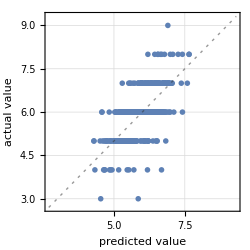
Predictor Measurements
Predictor method | GradientBoostedTrees
Number of test examples | 490
Standard deviation | 0.638 ± 0.027
Standard deviation baseline | 0.866 ± 0.029
R-squared | 0.458 ± 0.059
Mean cross entropy | 1.12 ± 0.084
Single evaluation time | 5.33 ms/example
Batch evaluation speed | 1.83 examples/ms
-Graphics- |

```mathematica
pm=PredictorMeasurements[p,testData]
```

### Standard NN

```mathematica
(* Or-Not architecture *)
standardNet=StandardNet[64,4]
```

NetGraph[<>]

```mathematica
result=TrainStandardNet[standardNet,trainData,testData];
```

```mathematica
trainedStandardNet=result["TrainedNet"]
```

NetGraph[<>]

```mathematica
NetMeasurements[trainedStandardNet,testData,{"RSquared"}]
```

{0.376726}

```mathematica
standardPredictions=NetPredict[trainedStandardNet,testData,"WineQuality"];
```

```mathematica
(*{MinMax[#["Prediction"]&/@standardPredictions],MinMax[#["Target"]&/@standardPredictions]}*)
```

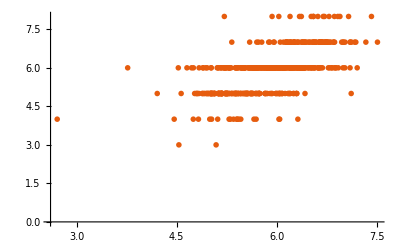

```mathematica
ListPlot[Values/@standardPredictions,PlotRange->All,PlotTheme->{"DarkColor","OpenMarkers"}]
```

```mathematica
standardWeights=GetStandardWeights[trainedStandardNet];
```

```mathematica
standardNetSize=Quantity[Length[standardWeights]*32/1024.0,"Kilobytes"]
```

536. kB

## A neural logic network

```mathematica
(*{softNet,hardNet}=NeuralLogicNet[NeuralLogicPredictor[32]];*)
(*{softNet,hardNet}=NeuralLogicNet[NeuralLogicPredictor[256,512,2]];*)
{softNet,hardNet}=NeuralLogicNet[NeuralLogicPredictor[(*numConditions*)64,(*conditionSize*)1,(*actionSize*)8]];
```

```mathematica
NetFlatten[softNet,Infinity]
```

NetGraph[<>]

```mathematica
result=Block[{td=Take[trainData,All],vd=testData},
TrainNeuralLogicNet[softNet,td,vd]
]
```

$Failed

```mathematica
trainedNeuralLogicNet=result["TrainedNet"];
```

```mathematica
NetMeasurements[trainedNeuralLogicNet,testData,{"RSquared"}]
```

{0.0652296}

```mathematica
hnf=HardNetFunction[hardNet,trainedNeuralLogicNet];
(* Jump ahead to predictions to save time *)
hnbe=HardNetBooleanExpression[hnf,neuralLogicInputSize]
```

```mathematica
predictions=NeuralLogicPredict[testData,encoders,"WineQuality",hnf,neuralLogicFeatureLayer];
```

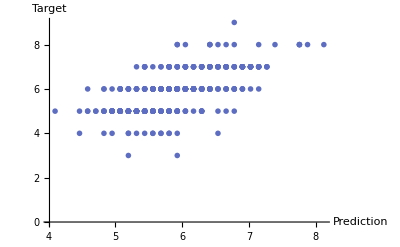

```mathematica
ListPlot[{{Missing[]},predictions},AxesLabel->Automatic,PlotRange->All,PlotTheme->{"DarkColor","OpenMarkers"}]
```

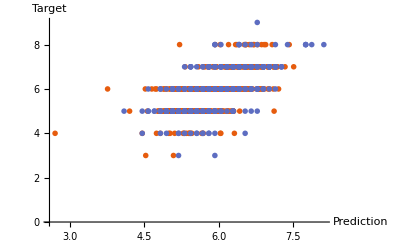

```mathematica
ListPlot[{standardPredictions,predictions},AxesLabel->Automatic,PlotRange->All,PlotTheme->{"DarkColor","OpenMarkers"}]
```

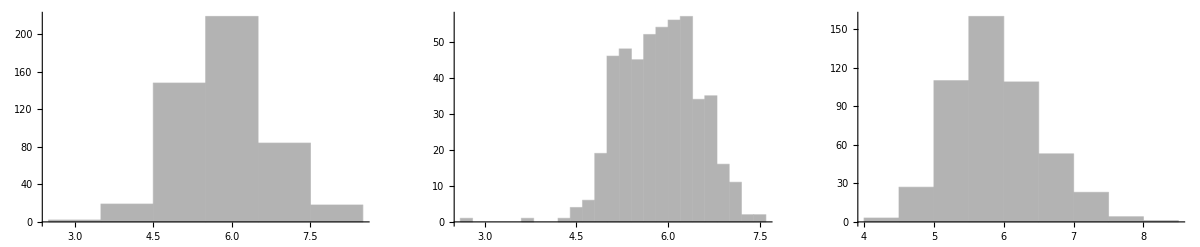

```mathematica
GraphicsRow[Histogram[#,PlotRange->All,PlotTheme->"Monochrome"]&/@{#["Target"]&/@standardPredictions,#["Prediction"]&/@standardPredictions,#["Prediction"]&/@predictions}]
```

```mathematica
neuralLogicWeights=GetNeuralLogicWeights[result["TrainedNet"]];
```

```mathematica
neuralLogicNetSize=Quantity[Length[neuralLogicWeights]/8/1024//N,"Kilobytes"]
```

8.875 kB

```mathematica
#["NumBits"]&/@KeyDrop[encoders,"WineQuality"]
```

<|FixedAcidity→35,VolatileAcidity→62,CitricAcid→42,ResidualSugar→155,Chlorides→79,FreeSulfurDioxide→65,TotalSulfurDioxide→126,Density→430,PH→51,Sulphates→39,Alcohol→51|>

```mathematica
encoderSize=Quantity[Total[Values[#["NumBits"]&/@KeyDrop[encoders,"WineQuality"]]]*32.0/1024,"Kilobytes"]
```

35.4688 kB

```mathematica
totalNeuralLogicNetSize=neuralLogicNetSize+encoderSize
```

44.3438 kB

```mathematica
standardNetSize
```

536. kB

## Notes

```mathematica
neuralLogicPredictions=NetPredict[trainedNeuralLogicNet,testData,"WineQuality"];
```

```mathematica
{MinMax[#["Prediction"]&/@neuralLogicPredictions],MinMax[#["Target"]&/@neuralLogicPredictions]}
```

{{4.52344,8.05781},{3,9}}

```mathematica
ListPlot[Values/@neuralLogicPredictions]
```